# Rotating star

Author : Martin Horvat, June 2016

## Potential of the rotating star

```mathematica
Clear[Omega];
Omega[x_,y_,z_,omega_]:=1/Sqrt[x^2+y^2+z^2]+1/2 omega^2(x^2+y^2)
```

```mathematica
Clear[DOmega];
DOmega[x_,y_,z_,omega_]=D[Omega[x,y,z,omega],{{x,y,z}}]
```

{omega^2 x-x/((x^2+y^2+z^2)^(3/2)),omega^2 y-y/((x^2+y^2+z^2)^(3/2)),-z/((x^2+y^2+z^2)^(3/2))}

```mathematica
Simplify[DOmega[0,0,1/Omega0,omega],Omega0>0]
```

{0,0,-Omega0^2}

## Plots

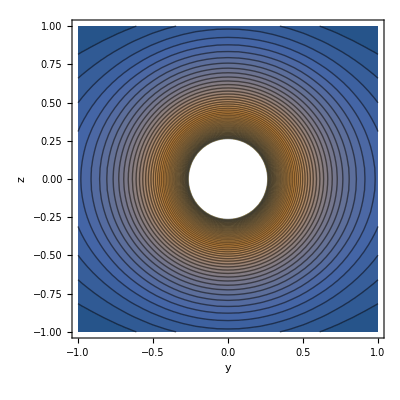

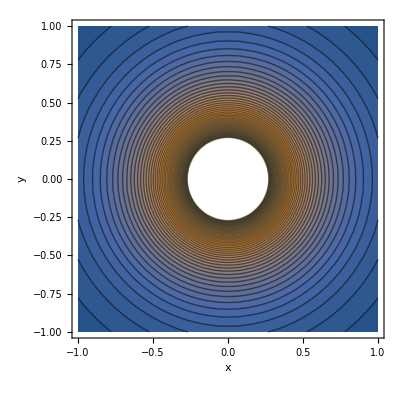

```mathematica
ContourPlot[Omega[0,y,z,0.5],{y,-1,1},{z,-1,1},Contours->50,AxesLabel->{"y","z"}]
ContourPlot[Omega[x,y,0,0.5],{x,-1,1},{y,-1,1},Contours->50,AxesLabel->{"x","y"}]
```

```mathematica
Plot[Omega[x,0,0,1],{x,-2,2}]
```

## z= v/Omega, z=v/Omega, dv/du

```mathematica
v[s_,b_]:= Sqrt[-s(1-b*s)^2+1]/(1-b*s);
dvds[s_,b_]=-FullSimplify[D[v[s,b],s]]
```

-(-1+b (2+s (3+b s (-3+b s))))/(2 (-1+b s)^2 √(1-s (-1+b s)^2))

```mathematica
Series[v[s,b],{b,0,2}]
```

√(1-s)+(s b)/(√(1-s))+((-2 s^2+3 s^3) b^2)/(2 √(1-s) (-1+s))+O[b]^3

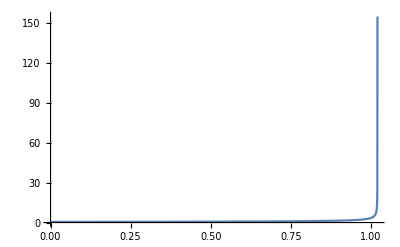

```mathematica
Block[{s0,u0,b},
b=0.01;
u0=Min[Select[u/.NSolve[b*u^3-u+1==0,u,Reals],#>0&]];
s0=u0*u0;
Plot[dvds[s,b],{s,0,s0*0.99999},PlotRange->All]
]
```

```mathematica
Block[{b,s,s0,u0,u},
b=0.0001;

u0=Min[Select[u/.NSolve[b*u^3-u+1==0,u,Reals],#>0&]];

s0=u0*u0;

NIntegrate[{4Pi*Sqrt[s*dvds[s,b]^2+1/4],2Pi*s*dvds[s,b]},{s,0,s0}]
]
```

{12.568,4.18963}

## series, s =u^2, t=v^2

t [s_]= 1/(1 - b s)^2 - s

```mathematica
S[t_,b_]=Normal[FullSimplify[InverseSeries[Series[1-1/(1 - b s)^2 + s,{s,0,3}],t]]]
```

t/(1-2 b)-(3 b^2 t^2)/(-1+2 b)^3-(2 b^3 (2+5 b) t^3)/(-1+2 b)^5

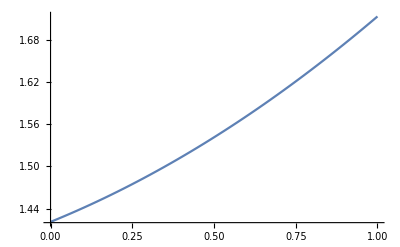

```mathematica
Plot[S[t,4/27.]/t,{t,0,1}]
```

```mathematica
S[1,0.1]
```

1.32385

```mathematica
Solve[1/Sqrt[s+v]+b s ==1/.{b->0.1,v->0},s]
```

{{s→1.33049},{s→5.87394}}

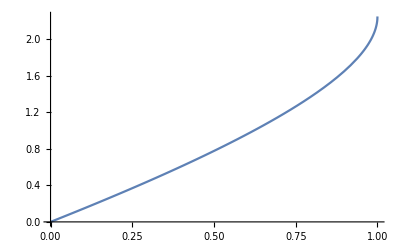

```mathematica
Plot[Min[s/.Solve[1/Sqrt[s+1-t]+4/27 s ==1,s]],{t,0,1}]
```

## Via Integration

```mathematica
A=s'[t]/.FullSimplify[Solve[D[1/Sqrt[s[t]+t]+b s[t],t]==0,s'[t]]][[1]]
```

1/(-1+2 b t √(t+s[t])+2 b s[t] √(t+s[t]))

```mathematica
Simplify[A/.√(t+s[t])->q]/.{t->1,s[t]->0,q->1,b->0.1}
```

-1.25